# S2S Data Cutting

## Slide Show Subtitle

BX Pan
2017.9.27

Environment Setting

```mathematica
controlDirectory="/Volumes/lambda/Data/S2S/Control/";
pertubationDirectory="/Volumes/lambda/Data/S2S/Pertubation/";
```

```mathematica
polygon=Block[{westconus},
	westconus=Block[{ow,ca},
	ow=Import["/Users/lambda/Documents/Data/GeoDivision/CONUS/oregonwashington.mx"];
	ca=Import["/Users/lambda/Documents/Data/GeoDivision/CONUS/california.mx"];
	Polygon[Flatten[{ow[[1]],ca[[1]]},1]]];
	westconus[[1]]];
(*polygon in the form of {subpoly1,subpoly2,...},subpoly in th form of {{long1,lat1},{long2,lat2}...}*)
```

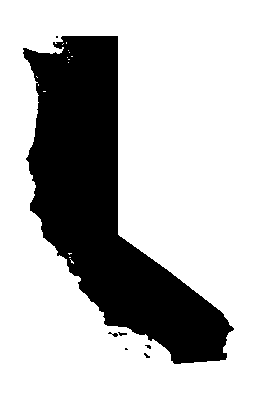

```mathematica
Graphics[Polygon[polygon]]
```

S2SCut

```mathematica
S2Scut[polygon_,dataset_]:=Block[{points,sample,result,files,sindex,scale},
 SetDirectory["/Volumes/lambda/Data/S2S/Control/"<>dataset];
 sample=FileNames["*.nc"][[1]];
 points=Block[{s2sprecip,s2slat,s2slon,s2stime,p,indexes},
	{s2sprecip,s2slat,s2slon,s2stime}=Map[Import[sample,{"Datasets",#}]&,{"tp","latitude","longitude","time"}];
    p=Block[{InOrOut,grids},
        InOrOut[point_]:=Block[{singletest},
			singletest[poly_] := Round[(Total@ Mod[(# - RotateRight[#]) &@(ArcTan @@ (point - #) & /@ poly), 2 Pi, -Pi]/2/Pi)] != 0;
			(Map[singletest,polygon])/.List->Or];
        grids=Block[{scope=Map[MinMax,Transpose[Flatten[polygon,1]]],lat,lon},
            lat=Select[s2slat,And[#<=scope[[2,2]], #>=scope[[2,1]]]&];
            lon=Select[s2slon,And[#<=scope[[1,2]], #>=scope[[1,1]]]&];
        Table[Table[{lat[[i]],lon[[j]]},{j,Length[lon]}],{i,Length[lat]}]];
        Select[Flatten[grids,1],InOrOut[Reverse[#]]&]];
    indexes=Block[{grids=Table[Table[{s2slat[[i]],s2slon[[j]]},{j,Length[s2slon]}],{i,Length[s2slat]}]},
        Map[Position[grids,#][[1]]&,p]];
    indexes];
 sindex=Position[Map[Flatten[#/.Rule->List]&,Import[sample,"Annotations"]],
	_?(MemberQ[#,"Total Precipitation"]&)][[1,1]];
 files=FileNames["*.nc"];
 scale=Map[Import[#,"Annotations"][[sindex,1;;2,2]]&,files];
 result=Block[{raw=Map[Block[{d=Import[#,{"Datasets","tp"}]},
          Table[d[[;;,points[[jj,1]],points[[jj,2]]]],{jj,Length[points]}]]&,files]},
          Table[raw[[i]]*scale[[i,1]]+scale[[i,2]],{i,Length[scale]}]];
 Export[dataset<>".mx",result];
 result];
```

```mathematica
SetDirectory["/Volumes/lambda/Data/S2S/Control/"];
names=FileNames[][[{1,3,4,5,6,7,8,9,10,11}]]
```

```mathematica
PS2Scut[polygon_,dataset_]:=Block[{points,sample,result,files,sindex,scale},
 SetDirectory["/Volumes/lambda/Data/S2S/Pertubation/"<>dataset];
 files=FileNames["*.nc"];
 sample=files[[1]];
 points=Block[{s2sprecip,s2slat,s2slon,s2stime,p,indexes},
	{s2sprecip,s2slat,s2slon,s2stime}=Map[Import[sample,{"Datasets",#}]&,{"tp","latitude","longitude","time"}];
    p=Block[{InOrOut,grids},
        InOrOut[point_]:=Block[{singletest},
			singletest[poly_] := Round[(Total@ Mod[(# - RotateRight[#]) &@(ArcTan @@ (point - #) & /@ poly), 2 Pi, -Pi]/2/Pi)] != 0;
			(Map[singletest,polygon])/.List->Or];
        grids=Block[{scope=Map[MinMax,Transpose[Flatten[polygon,1]]],lat,lon},
            lat=Select[s2slat,And[#<=scope[[2,2]], #>=scope[[2,1]]]&];
            lon=Select[s2slon,And[#<=scope[[1,2]], #>=scope[[1,1]]]&];
        Table[Table[{lat[[i]],lon[[j]]},{j,Length[lon]}],{i,Length[lat]}]];
        Select[Flatten[grids,1],InOrOut[Reverse[#]]&]];
    indexes=Block[{grids=Table[Table[{s2slat[[i]],s2slon[[j]]},{j,Length[s2slon]}],{i,Length[s2slat]}]},
        Map[Position[grids,#][[1]]&,p]];
    indexes];
 sindex=Position[Map[Flatten[#/.Rule->List]&,Import[sample,"Annotations"]],
	_?(MemberQ[#,"Total Precipitation"]&)][[1,1]];
 scale=Map[Import[#,"Annotations"][[sindex,1;;2,2]]&,files];
 result=Block[{raw=Map[Block[{d=Import[#,{"Datasets","tp"}]},
          Table[d[[;;,;;,points[[jj,1]],points[[jj,2]]]],{jj,Length[points]}]]&,files]},
          Table[raw[[i]]*scale[[i,1]]+scale[[i,2]],{i,Length[scale]}]];
 Export[dataset<>"_pertubation.mx",result];
 result];
```

S2SPrune

```mathematica
S2SPrune[dataset_]:=Block[{control,pertubation,combine,result},
	SetDirectory["/Users/lambda/Documents/Research/S2SEvaluation/Data/"<>dataset];
	control=Import["*_control.mx"][[1]];
	pertubation=Import["*_pertubation.mx"][[1]];
	combine=Append[Table[pertubation[[;;,;;,;;,i]],{i,Dimensions[pertubation][[-1]]}],control];
	result=Table[If[i==1,combine[[;;,;;,;;,1]],combine[[;;,;;,;;,i]]-combine[[;;,;;,;;,i-1]]],
			{i,Dimensions[control][[-1]]}];
	Export[dataset<>"_simu.mx",result]];
```

```mathematica
datasets=Block[{},
	SetDirectory["/Users/lambda/Documents/Research/S2SEvaluation/Data"];
	FileNames[][[{1,2,10,11,12,13,14,15,16,17,19}]]]
```

{BoM,CMA,ECCC,ECMWF,HCMR,ISACCNR,JMA,KMA,MeteoFrance,NCEP,UKMO}

```mathematica
TableForm[Map[Block[{simu},
		SetDirectory["/Users/lambda/Documents/Research/S2SEvaluation/Data/"<>#];
		simu=Import[#<>"_simu.mx"];
		Flatten[{#,Dimensions[simu]}]]&,datasets],
		TableHeadings->{None,{"Dataset","Forecast Days","Ensemble Size","Starting Times","Grids"}},
		TableAlignments->Center]
```

Dataset | Forecast Days | Ensemble Size | Starting Times | Grids
BoM | 62 | 33 | 2376 | 13
CMA | 60 | 4 | 7665 | 33
ECCC | 32 | 4 | 1780 | 33
ECMWF | 46 | 11 | 2962 | 33
HCMR | 61 | 10 | 3268 | 33
ISACCNR | 31 | 1 | 2190 | 33
JMA | 34 | 5 | 1080 | 33
KMA | 60 | 3 | 660 | 33
MeteoFrance | 61 | 15 | 528 | 33
NCEP | 44 | 4 | 4380 | 33
UKMO | 60 | 3 | 1104 | 33

CPCCut

```mathematica
CPCCut[polygon,"BoM"];
```

```mathematica
CPCCut[polygon_,dataset_]:=Block[{s2slat,s2slon,cpclat,cpclon,size,points,indexes,files, DownScale,result},
	{s2slat,s2slon}=Block[{file},
		SetDirectory["/Volumes/lambda/Data/S2S/Control/"<>dataset];
		file=FileNames["*.nc"][[1]];
		Import[file,{"Datasets",{"latitude","longitude"}}]];
	{cpclat,cpclon}=Import["/Users/lambda/Documents/Data/Precipitation/CPC_Precipitation/global/precip.1979.nc",{"Datasets",{"lat","lon"}}];
	size={Round[Abs[s2slat[[2]]-s2slat[[1]]]/Abs[cpclat[[2]]-cpclat[[1]]]],
      Round[Abs[s2slon[[2]]-s2slon[[1]]]/Abs[cpclon[[2]]-cpclon[[1]]]]};
    points = Block[{InOrOut, grids},
           InOrOut[point_] := Block[{singletest},
     			singletest[poly_] := Round[(Total@ Mod[(# - RotateRight[#]) &@(ArcTan @@ (point - #) & /@ poly), 2 Pi, -Pi]/2/Pi)] != 0;
     			(Map[singletest, polygon]) /. List -> Or];
           grids = Block[{scope = Map[MinMax, Transpose[Flatten[polygon, 1]]], lat, lon},
                 lat = Select[s2slat, And[# <= scope[[2, 2]], # >= scope[[2, 1]]] &];
                 lon = Select[s2slon, And[# <= scope[[1, 2]], # >= scope[[1, 1]]] &];
             Table[Table[{lat[[i]], lon[[j]]}, {j, Length[lon]}], {i, Length[lat]}]];
           Select[Flatten[grids, 1], InOrOut[Reverse[#]] &]];
    indexes = Block[{grids = Table[Table[{s2slat[[i]], s2slon[[j]]}, {j, Length[s2slon]}], {i, Length[s2slat]}]},
           Map[Position[grids, #][[1]] &, points]];
    DownScale[data_,ratio_]:=Block[{convoluter},
			(* This Function performs spacial average downscaling of 2D data through uniform convolution ratio is kind like {5,4}*) 
			convoluter = Block[{net},
   			net = NetInitialize[ConvolutionLayer[1, ratio, "Stride" -> ratio, 
   						"Input" -> Flatten[{1, Dimensions[data]}]]];
               NetReplacePart[net, {"Weights" -> ConstantArray[1./(ratio/.List->Times), Flatten[{1, 1, ratio}]]}]];
            (convoluter@{data})[[1]]];
    files=Block[{},
       SetDirectory["/Users/lambda/Documents/Data/Precipitation/CPC_Precipitation/global"];
       FileNames["*.nc"]];
    result=Map[Block[{data=Import[#,{"Datasets","precip"}]},
       data=Map[DownScale[#,size]&,data];
       Map[data[[;; , #[[1]], #[[2]]]] &, indexes]]&,files];
    Export["/Users/lambda/Documents/Research/S2SEvaluation/Data/"<>dataset<>"/CPC.mx",result]];
```

CPC Temporal Prune

```mathematica
CPCPrune[dataset_]:=Block[{time,cpctime,result,cpc},
	cpc=Block[{tempt=Import["/Users/lambda/Documents/Research/S2SEvaluation/Data/CPC.mx"]},
		Flatten[Map[Transpose,tempt],1]];
	cpctime=Range[Length[cpc]];
	SetDirectory["/Users/lambda/Documents/Research/S2SEvaluation/Data/"<>dataset];
	time=Block[{start,duration},
		start=Map[DateDifference[{1978,12,31},#][[1]]&,Import[dataset<>"_control_time.mx"]];
		duration=Dimensions[Import[dataset<>"_control.mx"]][[-1]]-1;
		Map[{#,#+duration}&,start]];
	result=Map[cpc[[#[[1]];;#[[2]],;;]]&,time];
	Export[dataset<>"_cpc.mx",result]];
```

```mathematica
dataset="HCMR";
cpc=Import["/Users/lambda/Documents/Research/S2SEvaluation/Data/"<>dataset<>"/"<>dataset<>"_cpc.mx"];
```

GeoPoints

```mathematica
S2SGrids[polygon_,dataset_]:=Block[{points,sample,result,files,sindex,scale},
 SetDirectory["/Volumes/lambda/Data/S2S/Control/"<>dataset];
 sample=FileNames["*.nc"][[1]];
 points=Block[{s2sprecip,s2slat,s2slon,s2stime,p,indexes},
	{s2sprecip,s2slat,s2slon,s2stime}=Map[Import[sample,{"Datasets",#}]&,{"tp","latitude","longitude","time"}];
    p=Block[{InOrOut,grids},
        InOrOut[point_]:=Block[{singletest},
			singletest[poly_] := Round[(Total@ Mod[(# - RotateRight[#]) &@(ArcTan @@ (point - #) & /@ poly), 2 Pi, -Pi]/2/Pi)] != 0;
			(Map[singletest,polygon])/.List->Or];
        grids=Block[{scope=Map[MinMax,Transpose[Flatten[polygon,1]]],lat,lon},
            lat=Select[s2slat,And[#<=scope[[2,2]], #>=scope[[2,1]]]&];
            lon=Select[s2slon,And[#<=scope[[1,2]], #>=scope[[1,1]]]&];
        Table[Table[{lat[[i]],lon[[j]]},{j,Length[lon]}],{i,Length[lat]}]];
        Select[Flatten[grids,1],InOrOut[Reverse[#]]&]];
    indexes=Block[{grids=Table[Table[{s2slat[[i]],s2slon[[j]]},{j,Length[s2slon]}],{i,Length[s2slat]}]},
        Map[Position[grids,#][[1]]&,p]];
    p];
  Export["/Users/lambda/Documents/Research/S2SEvaluation/Data/"<>dataset<>"/"<>dataset<>"_grids.mx",points];
  points];
```

```mathematica
Map[S2SGrids[polygon,#]&,models];
```